## Calculation of spindle torques

## define geometrical functions

Distance between a centrosome and the contour

```mathematica
dc[θ_,ϕ_]=Sqrt[R^2+lc^2-2 R lc Cos[θ-ϕ]];
```

Torque integrand (function I(theta) in the Supplementary Text

```mathematica
TorqueInt[θ_, ϕ_, R_,lc_] = R lc Sin[θ-ϕ] (R-lc Cos[θ-ϕ])/dc[θ,ϕ]^(3)
```

(lc R (R-lc Cos[θ-ϕ]) Sin[θ-ϕ])/((lc^2+R^2-2 lc R Cos[θ-ϕ])^(3/2))

```mathematica
Integrate[TorqueInt[θ, ϕ, R,lc],{θ,0,2Pi}]
```

0

Angle to be added or substracted to phi to obtain the region of integration

```mathematica
BoundaryValue[lm_,R_,lc_]=ArcCos[(R^2+lc^2-lm^2)/(2 lc R)]
```

ArcCos[(lc^2-lm^2+R^2)/(2 lc R)]

When the argument of the arccos is equal to -1: lm=l_c+R and the solution is pi, i.e. all points are reachable
 When the argument of the arccos is equal to 1: lm=l_c-R and the solution is 0, i.e. a single point is reachable

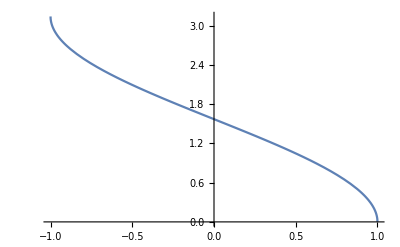

```mathematica
Plot[ArcCos[x],{x,-1,1}]
```

A gaussian profile of force with angular width w (use von Mises Distribution)

```mathematica
ForceDistribution[θ_,w_]=1/(4 Pi BesselI[0,1/w^2])*(Exp[-Cos[θ]/w^2] + Exp[Cos[θ]/w^2] )
```

(ⅇ^(-Cos[θ]/w^2)+ⅇ^(Cos[θ]/w^2))/(4 π BesselI[0,1/w^2])

Verify that the integral is 1

```mathematica
Integrate[ForceDistribution[θ,w],{θ,-Pi,Pi}]
```

1

Introduce a numerical version - a trick to avoid dealing numerically with ratios of large numbers; by plugging the Bessel function in the exponential

```mathematica
ForceDistributionNumerical[θ_?NumberQ,w_?NumberQ]:=1/(4 Pi )*(Exp[SetPrecision[-Cos[θ]/w^2 - Log[BesselI[0,1/w^2]],10]] + Exp[SetPrecision[Cos[θ]/w^2- Log[BesselI[0,1/w^2]],10]] )
```

Plot a few examples of force distribution

General::munfl: Exp[-10000.] is too small to represent as a normalized machine number; precision may be lost.

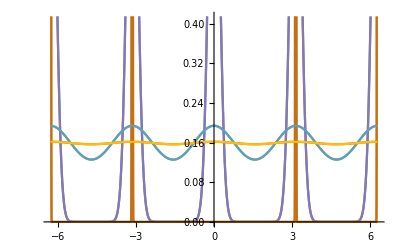

```mathematica
Plot[{ForceDistribution[θ,0.2],ForceDistribution[θ,0.01],ForceDistribution[θ,1],ForceDistribution[θ,2],ForceDistributionNumerical[θ,0.2],ForceDistributionNumerical[θ,0.01],ForceDistributionNumerical[θ,1],ForceDistributionNumerical[θ,2]},{θ,-2 Pi,2Pi}]
```

Define torque value

```mathematica
TorqueValue[ϕ_,lm_,R_,lc_,w_]:=NIntegrate[TorqueInt[θ,ϕ, R,lc] *ForceDistributionNumerical[θ,w],{θ,ϕ-BoundaryValue[lm,R,lc],ϕ+BoundaryValue[lm,R,lc]},WorkingPrecision->10,AccuracyGoal->8]
```

## Stability analysis and phase diagram

```mathematica
Ifunction[θ_,R_,lc_]= R lc Sin[θ] (R-lc Cos[θ])/(Sqrt[R^2+lc^2-2 R lc Cos[θ]])^(3)
```

(lc R (R-lc Cos[θ]) Sin[θ])/((lc^2+R^2-2 lc R Cos[θ])^(3/2))

```mathematica
DIfunction[θ_,R_,lc_]= FullSimplify[D[Ifunction[θ,R,lc],θ]]
```

(lc R (R (11 lc^2+4 R^2) Cos[θ]-2 lc (2 lc^2+R^2) Cos[2 θ]+lc R (-10 R+lc Cos[3 θ])))/(4 (lc^2+R^2-2 lc R Cos[θ])^(5/2))

Function which gives the stability in ϕ =0

```mathematica
StabilityFunction[lm_,R_,lc_,w_] :=  Ifunction[BoundaryValue[lm,R,lc],R,lc]*ForceDistributionNumerical[BoundaryValue[lm,R,lc],w] -   Ifunction[-BoundaryValue[lm,R,lc],R,lc]*ForceDistributionNumerical[-BoundaryValue[lm,R,lc],w] -NIntegrate[DIfunction[θ,R,lc]*ForceDistributionNumerical[θ,w],{θ,-BoundaryValue[lm,R,lc],BoundaryValue[lm,R,lc]},WorkingPrecision->10,AccuracyGoal->10]
```

Function which the stability in ϕ=Pi/2

```mathematica
StabilityFunctionPihalf[lm_,R_,lc_,w_] :=  Ifunction[BoundaryValue[lm,R,lc],R,lc]*ForceDistributionNumerical[Pi/2+BoundaryValue[lm,R,lc],w] -   Ifunction[-BoundaryValue[lm,R,lc],R,lc]*ForceDistributionNumerical[Pi/2-BoundaryValue[lm,R,lc],w] -NIntegrate[DIfunction[θ-Pi/2,R,lc]*ForceDistributionNumerical[θ,w],{θ,Pi/2-BoundaryValue[lm,R,lc],Pi/2+BoundaryValue[lm,R,lc]},WorkingPrecision->10,AccuracyGoal->10]
```

The ratio gives the stability of a combination of pulling and pushing forces

```mathematica
StabilityFunction[0.6,1,0.5,0.7]/StabilityFunction[0.6,1,0.5,0.5]
```

0.381363

Parameters: R is set to 1; other lengths are normalized to the cell radius r=8.9um

```mathematica
Rvalue  = 1;
lcvalue  =5.4/8.9; 
lmvalue = 4.1/8.9;
wplusvalue = 1.14; (*extracted from Numa analysis*)
```

Value of θm and 2θm in degrees

```mathematica
180/Pi * BoundaryValue[lmvalue,Rvalue ,lcvalue]
2* 180/Pi * BoundaryValue[lmvalue,Rvalue ,lcvalue]
```

17.7192

35.4385

Plot  the corresponding phase diagram
The x axis is wminus, the width of the pushing force region
The y axis is f-/f+, the ratio of the magnitude of the pushing force region and the pulling force region

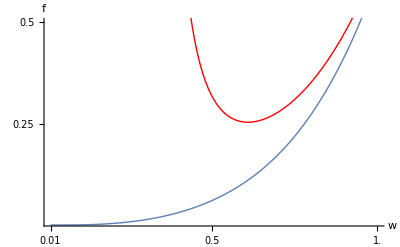

```mathematica
phasediagram=Show[Plot[StabilityFunction[lmvalue,Rvalue,lcvalue,wplusvalue ]/StabilityFunction[lmvalue,Rvalue,lcvalue,w],{w,0.01,1.0},PlotStyle->Thick],Plot[StabilityFunctionPihalf[lmvalue,Rvalue,lcvalue,wplusvalue ]/StabilityFunctionPihalf[lmvalue,Rvalue,lcvalue,w],{w,0.1,1.0},PlotStyle->{Red,Thick}],AxesOrigin->{0.01,0},PlotRange->{0.01,0.5}, Ticks->{{0.01,0.5,1.0},{0,0.25,0.5}},TicksStyle->Directive[Black,15],AxesLabel->{w,f},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]];
Export["phasediagram.pdf",phasediagram,"PDF","AllowRasterization"->False];
```

Examples: for wminus=0.5, look at the predicted threshold, and look at the corresponding predicted torque profiles

0.0630834

0.317221

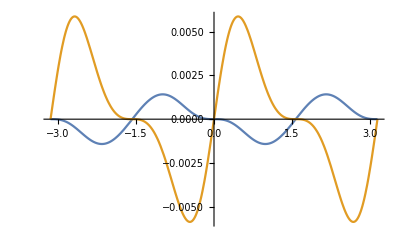

```mathematica
wminustest=0.5;
threshold0=StabilityFunction[lmvalue,Rvalue,lcvalue,wplusvalue ]/StabilityFunction[lmvalue,Rvalue,lcvalue,wminustest ]
thresholdpihalf=StabilityFunctionPihalf[lmvalue,Rvalue,lcvalue,wplusvalue ]/StabilityFunctionPihalf[lmvalue,Rvalue,lcvalue,wminustest]
Plot[{TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wplusvalue]-threshold0 TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wminustest],TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wplusvalue]-thresholdpihalf TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wminustest]},{ϕ,-Pi,Pi}]
```

Profiles near the left of the diagram

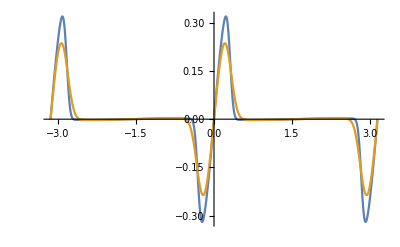

```mathematica
Plot[{TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wplusvalue]-1TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,0.05],TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wplusvalue]-1TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,0.1]},{ϕ,-Pi,Pi},PlotRange->All]
```

## Equilibrium spindle position as a function of the cortical force distribution

Function looking for zeros of a function

```mathematica
Options[RootsInRange]=Options[NDSolve];
RootsInRange[{f1_,f2_},{x0_,x1_,x2_},opts:OptionsPattern[]]:=Module[{x,y,t,s,f=Function[x0,Evaluate[f1-f2]],res},res=Reap[NDSolve[{x'[t]==1,x[x1]==x1,y[t]==f[t],WhenEvent[y[t]==0,Sow[s/.FindRoot[f[s],{s,t}],"zero"]]},{x[t],y[t]},{t,x1,x2},opts],"zero"][[2]];If[Length[res]==0,res,res[[1]]]];
RootsInRange[f1_==f2_,{t_,tmin_,tmax_},opts___]:=RootsInRange[{f1,f2},{t,tmin,tmax},opts]
```

Test that the function works

```mathematica
RootsInRange[Cos[2 ϕ]==0,{ϕ,0,Pi/2},WorkingPrecision->MachinePrecision]
Pi/4.0
```

{0.785398}

0.785398

To plot correctly different regions of the graphs, evaluate the stability lines

```mathematica
FirstStabilityThreshold01=StabilityFunction[lmvalue,Rvalue,lcvalue,wplusvalue ]/StabilityFunction[lmvalue,Rvalue,lcvalue,0.1]
FirstStabilityThreshold05=StabilityFunction[lmvalue,Rvalue,lcvalue,wplusvalue ]/StabilityFunction[lmvalue,Rvalue,lcvalue,0.5]
SecondStabilityThreshold01=StabilityFunctionPihalf[lmvalue,Rvalue,lcvalue,wplusvalue ]/StabilityFunctionPihalf[lmvalue,Rvalue,lcvalue,0.1]
SecondStabilityThreshold05=StabilityFunctionPihalf[lmvalue,Rvalue,lcvalue,wplusvalue ]/StabilityFunctionPihalf[lmvalue,Rvalue,lcvalue,0.5]
```

0.00306887

0.0630834

2.45024×10^27

0.317221

Calculate table of torque values.
The idea is to define an interpolated function from these tables, which will then allow to find roots more quickly.
Some precision has to be set for the interpolation of the torque (PrecisionInterpolation) and some resolution for the plotting (PrecisionPlotting)

```mathematica
PrecisionInterpolation=10^(-4);
PrecisionPlotting=10^(-3);
```

```mathematica
wminustest = 0.1; 
TorqueContributionPulling=Table[{ϕ,TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wplusvalue]},{ϕ,-0.1,Pi/2+0.1,PrecisionInterpolation}];
TorqueContributionPushing=Table[{ϕ,TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wminustest]},{ϕ,-0.1,Pi/2+0.1,PrecisionInterpolation}];TorqueFunctionPulling1=Interpolation[TorqueContributionPulling];
TorqueFunctionPushing1=Interpolation[TorqueContributionPushing];
```

```mathematica
ExtractRoots[m_] :=RootsInRange[TorqueFunctionPulling1[ϕ]-m TorqueFunctionPushing1[ϕ]==0,{ϕ,-0.1,Pi/2-0.1},WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->8,MaxSteps->500000]
SolutionsToPlotwminus01 = Table[{m,ExtractRoots[m]},{m,FirstStabilityThreshold01+PrecisionPlotting,0.5,PrecisionPlotting}];
```

Do the same thing, for a different value of w-

```mathematica
wminustest = 0.5; (*larger value of w- for comparison*)
TorqueContributionPulling=Table[{ϕ,TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wplusvalue]},{ϕ,-0.1,Pi/2+0.15,PrecisionInterpolation}];
TorqueContributionPushing=Table[{ϕ,TorqueValue[ϕ,lmvalue,Rvalue,lcvalue,wminustest]},{ϕ,-0.1,Pi/2+0.15,PrecisionInterpolation}];TorqueFunctionPulling2=Interpolation[TorqueContributionPulling];
TorqueFunctionPushing2=Interpolation[TorqueContributionPushing];
```

```mathematica
ExtractRoots[m_] :=RootsInRange[TorqueFunctionPulling2[ϕ]-m TorqueFunctionPushing2[ϕ]==0,{ϕ,-0.1,Pi/2+0.1},PrecisionGoal->8,AccuracyGoal->8,MaxSteps->500000]
SolutionsToPlotwminus05 = Table[{m,ExtractRoots[m]},{m,FirstStabilityThreshold05+PrecisionPlotting,SecondStabilityThreshold05-PrecisionPlotting,PrecisionPlotting}];
```

Plot and save stable steady-state solutions for ϕ

```mathematica
FullTable01=Join[Table[{m,0},{m,0,FirstStabilityThreshold01,PrecisionPlotting}],Table[{SolutionsToPlotwminus01[[i]][[1]],SolutionsToPlotwminus01[[i]][[2]][[2]]},{i,1,Length[SolutionsToPlotwminus01]}]];
FullTable05=Join[Table[{m,0},{m,0,FirstStabilityThreshold05,PrecisionPlotting}],Table[{SolutionsToPlotwminus05[[i]][[1]],SolutionsToPlotwminus05[[i]][[2]][[2]]},{i,1,Length[SolutionsToPlotwminus05]}],Table[{m,Pi/2},{m,SecondStabilityThreshold05,0.5,PrecisionPlotting}]];
```

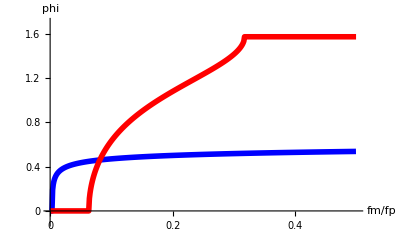

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

SteadyStateAnglePlot.pdf

```mathematica
SteadyStateAnglePlot=ListPlot[{FullTable01,FullTable05},Joined->True,PlotStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}},PlotRange->{{0,0.5},{-0.1,1.7}},Ticks->{{0,0.2,0.4},{0,0.2,0.4,0.6,0.8,1.0,1.2,1.4,1.6}},TicksStyle->Directive[Black,15],AxesLabel->{fm/fp,phi},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["SteadyStateAnglePlot.pdf",SteadyStateAnglePlot,"PDF","AllowRasterization"->False]
```

## Torque as a function of angle

Value of lc and lm in um, divided by the cell radius, which is used here as normalisation

```mathematica
lcvalue  =5.4/8.9; 
lmvalue = 4.1/8.9;
Rvalue=1.0;
```

Parameters for the force distribution function, obtained from fit to experimental data

```mathematica
bNuma= 7.237;
wNuma= 1.139;
amyosinbipolar=1.06;
bmyosinbipolar = 0.125;
wmyosinbipolar = 0.1004;
amyosinglobal=1.0675;
```

Define a new torque value which can be used with a force distribution which contains a product of two distributions

First introduced a normalized Numa force distribution, with a substraction which corresponds to the assumption that there is no cortical pulling force at the equator
Also introduce profiles resulting from activated myosin profiles

```mathematica
intNuma=NIntegrate[bNuma ForceDistribution[θ,wNuma]-1.0,{θ,0,2Pi}]
gN[θ_]=(bNuma ForceDistribution[θ,wNuma]-1.0)/intNuma;
gMbipolar[θ_]=(amyosinbipolar+bmyosinbipolar* ForceDistribution[θ,wmyosinbipolar]-1)/bmyosinbipolar;
gMglobal[θ_]=(amyosinglobal-1)/bmyosinbipolar;
```

0.953815

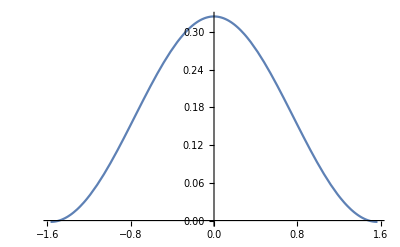

```mathematica
Plot[gN[θ],{θ,-Pi/2,Pi/2},AxesOrigin->{0,0}]
```

Perturbed myosin profiles

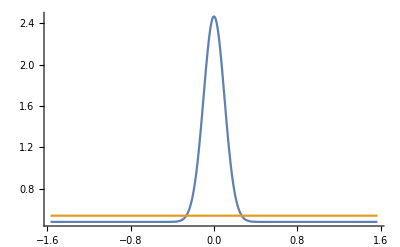

```mathematica
Plot[{gMbipolar[θ],gMglobal[θ]},{θ,-Pi/2,Pi/2},AxesOrigin->{0,0},PlotRange->All]
```

Calculate torque for different conditions

```mathematica
TorqueValueNuma[ϕ_,lm_,R_,lc_]:=NIntegrate[TorqueInt[θ,ϕ, R,lc] *gN[θ],{θ,ϕ-BoundaryValue[lm,R,lc],ϕ+BoundaryValue[lm,R,lc]},WorkingPrecision->10,AccuracyGoal->8]
TorqueValueMbipolar[ϕ_?NumberQ,lm_?NumberQ,R_?NumberQ,lc_?NumberQ,myosinfactor_?NumberQ]:=NIntegrate[TorqueInt[θ,ϕ, R,lc] *gN[θ]*(1-myosinfactor*gMbipolar[θ]),{θ,ϕ-BoundaryValue[lm,R,lc],ϕ+BoundaryValue[lm,R,lc]},WorkingPrecision->10,PrecisionGoal->8,AccuracyGoal->8]
TorqueValueMglobal[ϕ_?NumberQ,lm_?NumberQ,R_?NumberQ,lc_?NumberQ,myosinfactor_?NumberQ]:=NIntegrate[TorqueInt[θ,ϕ, R,lc] *gN[θ]*(1-myosinfactor*gMglobal[θ]),{θ,ϕ-BoundaryValue[lm,R,lc],ϕ+BoundaryValue[lm,R,lc]},WorkingPrecision->10,PrecisionGoal->8,AccuracyGoal->8]
```

The myosin factor introduced here is used to modulate the relative contributions of Numa and Myosin

```mathematica
myosinfactor = 2.2
```

2.2

Actual force distributions with this myosin factor; we can see that they become negative

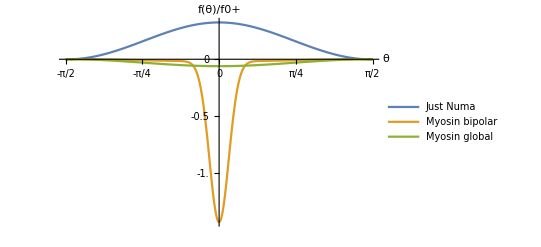

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

ForceDensityPlots.pdf

```mathematica
ForceDensityPlots=Plot[{gN[θ], gN[θ]*(1-myosinfactor*gMbipolar[θ]),gN[θ]*(1-myosinfactor*gMglobal[θ])},{θ,-Pi/2,Pi/2},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{θ,"f(θ)/f0+"},PlotLegends->{"Just Numa", "Myosin bipolar",  "Myosin global"},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-1.0,-0.5,0,0.5,1.0}},TicksStyle->Directive[Black,15],LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["ForceDensityPlots.pdf",ForceDensityPlots ,"PDF","AllowRasterization"->False]
```

Calculate the corresponding torque profiles

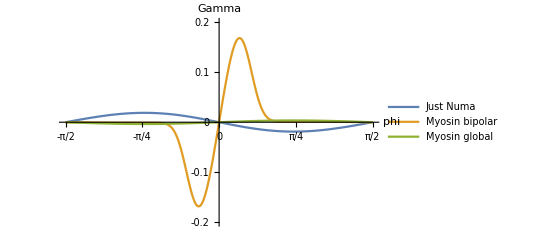

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

TorquePlots.pdf

```mathematica
TorquePlots = Plot[{TorqueValueNuma[ϕ,lmvalue,Rvalue,lcvalue], TorqueValueMbipolar[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor ],
TorqueValueMglobal[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor]
},{ϕ,-Pi/2,Pi/2},PlotLegends->{"Just Numa", "Myosin bipolar",  "Myosin global"},PlotRange->{-0.2,0.2},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-0.2,-0.1, 0, 0.1,0.2}},TicksStyle->Directive[Black,15],AxesLabel->{phi,Gamma},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["TorquePlots.pdf",TorquePlots ,"PDF","AllowRasterization"->False]
```

Save separate plots for the torques in different conditions

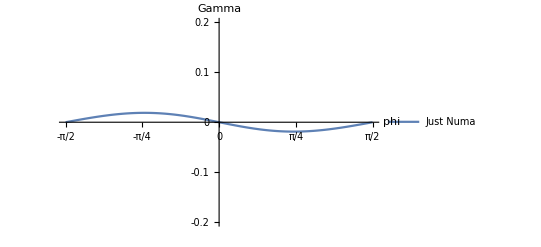

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

TorquePlotNuma.pdf

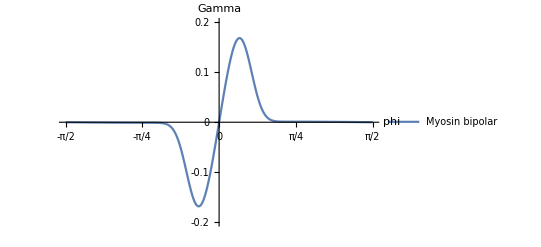

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

TorquePlotMbipolar.pdf

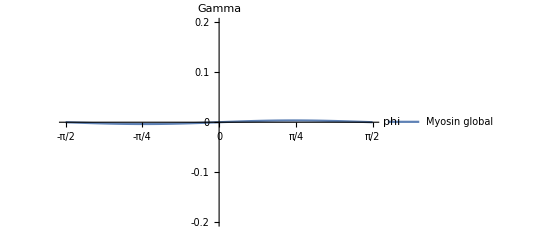

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

TorquePlotMglobal.pdf

```mathematica
TorquePlotNuma = Plot[{TorqueValueNuma[ϕ,lmvalue,Rvalue,lcvalue]
},{ϕ,-Pi/2,Pi/2},PlotLegends->{"Just Numa"},PlotRange->{-0.2,0.2},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-0.2,-0.1, 0, 0.1,0.2}},TicksStyle->Directive[Black,15],AxesLabel->{phi,Gamma},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["TorquePlotNuma.pdf",TorquePlotNuma ,"PDF","AllowRasterization"->False] 
TorquePlotMbipolar = Plot[{ TorqueValueMbipolar[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor ]
},{ϕ,-Pi/2,Pi/2},PlotLegends->{ "Myosin bipolar"},PlotRange->{-0.2,0.2},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-0.2,-0.1, 0, 0.1,0.2}},TicksStyle->Directive[Black,15],AxesLabel->{phi,Gamma},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["TorquePlotMbipolar.pdf",TorquePlotMbipolar ,"PDF","AllowRasterization"->False] 
TorquePlotMglobal = Plot[{TorqueValueMglobal[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor]
},{ϕ,-Pi/2,Pi/2},PlotLegends->{ "Myosin global"},PlotRange->{-0.2,0.2},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-0.2,-0.1, 0, 0.1,0.2}},TicksStyle->Directive[Black,15],AxesLabel->{phi,Gamma},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["TorquePlotMglobal.pdf",TorquePlotMglobal  ,"PDF","AllowRasterization"->False]
```

## Run spindle dynamics - stochastic (Fokker-Planck) - with experimentally determined diffusion and linear response time

Experimental measurements from mean squared rotations
The value of one over bar{tau} is in 1/minute
The measured Diffusion coefficient is in deg^2/min
It is then converted below in radians^2/min

```mathematica
Measuredoneoverbartauvalue  = 0.20508;
MeasuredDiffusionCoefficient = 19.265;
DiffusionCoefficientRad = MeasuredDiffusionCoefficient *(Pi/180)^2
Dvalue=DiffusionCoefficientRad ;
```

0.00586845

```mathematica
TorqueFunctionNuma[ϕ_?NumberQ]:= TorqueValueNuma[ϕ,lmvalue,Rvalue,lcvalue];
TorqueFunctionMbipolar[ϕ_?NumberQ]:=  TorqueValueMbipolar[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor];
TorqueFunctionMglobal[ϕ_?NumberQ]:=TorqueValueMglobal[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor];
```

Value of the linear torque response for the Numa case

```mathematica
Needs["NumericalCalculus`"]
LinearResponseFactor =-ND[TorqueFunctionNuma[ϕ],ϕ,0]
```

0.0392383

This allows to obtain an estimate of τ=γ/Γ0 by relating it to \bar{tau}”

```mathematica
τ=LinearResponseFactor/Measuredoneoverbartauvalue
```

0.191332

(Arbitrary) initial condition to solve the Fokker Planck equation

```mathematica
p0[ϕ_]=1/2*(PDF[VonMisesDistribution[0,1/0.1^2],ϕ]+PDF[VonMisesDistribution[0,1/0.1^2],Pi-ϕ]+PDF[VonMisesDistribution[0,1/0.1^2],ϕ+Pi]);
```

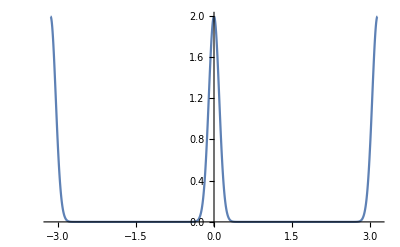

```mathematica
Plot[p0[ϕ],{ϕ,-Pi,Pi},PlotRange->All]
```

Interpolate the torque function to accelerate solving

```mathematica
PrecisionInterpolation=10^(-4);
```

```mathematica
TorqueFunctionNumaTable=Table[{ϕ,TorqueFunctionNuma[ϕ]},{ϕ,-3.5,3.5,PrecisionInterpolation}];
TorqueFunctionNumaInterp=Interpolation[TorqueFunctionNumaTable];
TorqueFunctionMbipolarTable=Table[{ϕ,TorqueFunctionMbipolar[ϕ]},{ϕ,-3.5,3.5,PrecisionInterpolation}];
TorqueFunctionMbipolarInterp=Interpolation[TorqueFunctionMbipolarTable];
TorqueFunctionMglobalTable=Table[{ϕ,TorqueFunctionMglobal[ϕ]},{ϕ,-3.5,3.5,PrecisionInterpolation}];
TorqueFunctionMglobalInterp=Interpolation[TorqueFunctionMglobalTable];
```

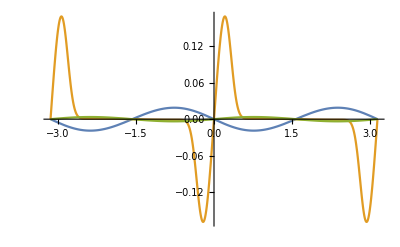

```mathematica
Plot[{TorqueFunctionNumaInterp[ϕ],TorqueFunctionMbipolarInterp[ϕ],TorqueFunctionMglobalInterp[ϕ]},{ϕ,-Pi,Pi},PlotRange->All]
```

First solve the evolution of the probability distribution for Numa
The corresponding equilibrium distribution will be used as the initialisation for other conditions

```mathematica
solFPNuma=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionNumaInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==p0[ϕ]},p[ϕ,t],{t,0,100},{ϕ,-Pi,Pi},PrecisionGoal->8,AccuracyGoal->6][[1]]
```

InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 100.}}, <>][ϕ,t]

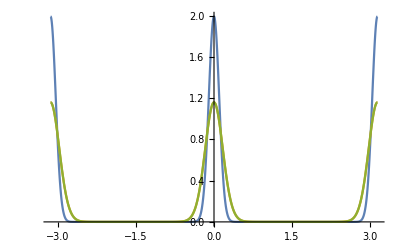

```mathematica
Plot[{solFPNuma/.{ϕ->ϕ2,t->0.},solFPNuma/.{ϕ->ϕ2,t->50},solFPNuma/.{ϕ->ϕ2,t->100}},{ϕ2,-Pi,Pi},PlotRange->All]
```

Restart with the equilibrium configuration with just Numa

```mathematica
newp0[ϕ2_]=solFPNuma/.{ϕ->ϕ2,t->100}
```

InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 100.}}, <>][ϕ2,100]

```mathematica
solFPNuma=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionNumaInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,12},{ϕ,-Pi,Pi}][[1]];
solFPMbipolar=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionMbipolarInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,12},{ϕ,-Pi,Pi}, Method->{"PDEDiscretization"->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->1000}}}][[1]];
solFPMglobal=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionMglobalInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,12},{ϕ,-Pi,Pi}][[1]];
```

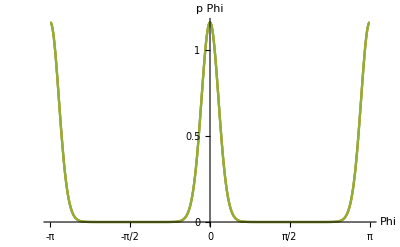

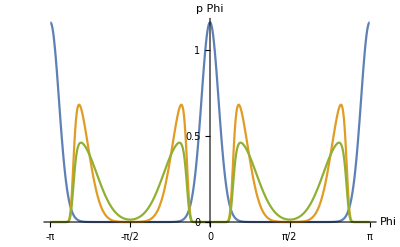

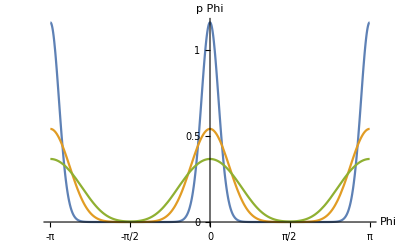

```mathematica
Plot[{solFPNuma/.{ϕ->ϕ2,t->0.},solFPNuma/.{ϕ->ϕ2,t->6},solFPNuma/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Plot[{solFPMbipolar/.{ϕ->ϕ2,t->0.},solFPMbipolar/.{ϕ->ϕ2,t->6},solFPMbipolar/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Plot[{solFPMglobal/.{ϕ->ϕ2,t->0.},solFPMglobal/.{ϕ->ϕ2,t->6},solFPMglobal/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
```

Plot the result between -Pi/2 and Pi/2

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

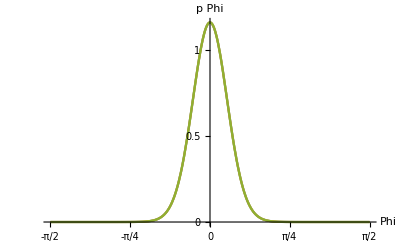

Probability_distributions_Numa.pdf

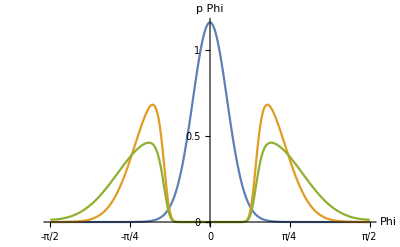

Probability_distributions_Myosin10X10.pdf

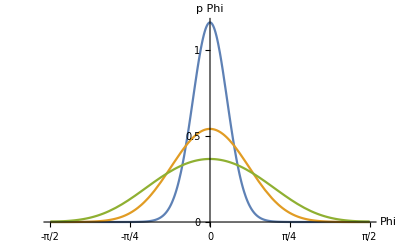

Probability_distributions_Myosinglobal.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
pdfJustNuma=Plot[{solFPNuma/.{ϕ->ϕ2,t->0.},solFPNuma/.{ϕ->ϕ2,t->6},solFPNuma/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi/2,Pi/2},PlotRange->All,Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Numa.pdf",pdfJustNuma,"PDF","AllowRasterization"->False] 
pdfmyosin10X10=Plot[{solFPMbipolar/.{ϕ->ϕ2,t->0.},solFPMbipolar/.{ϕ->ϕ2,t->6},solFPMbipolar/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi/2,Pi/2},PlotRange->All,Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Myosin10X10.pdf",pdfmyosin10X10,"PDF","AllowRasterization"->False] 
pdfmyosinglobal=Plot[{solFPMglobal/.{ϕ->ϕ2,t->0.},solFPMglobal/.{ϕ->ϕ2,t->6},solFPMglobal/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi/2,Pi/2},PlotRange->All,Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Myosinglobal.pdf",pdfmyosinglobal,"PDF","AllowRasterization"->False]
```

Plot the average value of ϕ between 0 and pi/2

```mathematica
avgabsϕNuma[t2_?NumberQ]:=NIntegrate[ϕ solFPNuma/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPNuma/.{t->t2},{ϕ,0,Pi/2}]
avgabsϕMbipolar[t2_?NumberQ]:=NIntegrate[ϕ solFPMbipolar/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPMbipolar/.{t->t2},{ϕ,0,Pi/2}]
avgabsϕMglobal[t2_?NumberQ]:=NIntegrate[ϕ solFPMglobal/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPMglobal/.{t->t2},{ϕ,0,Pi/2}]
```

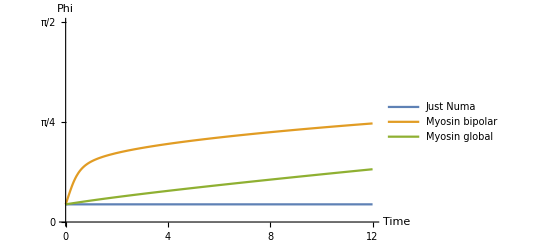

AverageAbsPhi.pdf

```mathematica
Plotaverageabsphi=Plot[{avgabsϕNuma[t],avgabsϕMbipolar[t],avgabsϕMglobal[t]},{t,0,12},PlotRange->{0,Pi/2},Ticks->{{0,4,8,12},{0,Pi/4,Pi/2}},TicksStyle->Directive[Black,15],AxesLabel->{Time,Phi},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15],PlotLegends->{"Just Numa", "Myosin bipolar", "Myosin global"}]
Export["AverageAbsPhi.pdf",Plotaverageabsphi ,"PDF","AllowRasterization"->False]
```

## Evolution on a longer time scale

```mathematica
solFPNuma=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionNumaInterp[ϕ] p[ϕ,t],ϕ]+τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,120},{ϕ,-Pi,Pi}][[1]];
solFPMbipolar=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionMbipolarInterp[ϕ] p[ϕ,t],ϕ]+τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,120},{ϕ,-Pi,Pi}, Method->{"PDEDiscretization"->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->1000}}}][[1]];
solFPMglobal=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionMglobalInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,120},{ϕ,-Pi,Pi}][[1]];
```

```mathematica
avgabsϕNuma[t2_?NumberQ]:=NIntegrate[ϕ solFPNuma/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPNuma/.{t->t2},{ϕ,0,Pi/2}]
avgabsϕMbipolar[t2_?NumberQ]:=NIntegrate[ϕ solFPMbipolar/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPMbipolar/.{t->t2},{ϕ,0,Pi/2}]
avgabsϕMglobal[t2_?NumberQ]:=NIntegrate[ϕ solFPMglobal/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPMglobal/.{t->t2},{ϕ,0,Pi/2}]
```

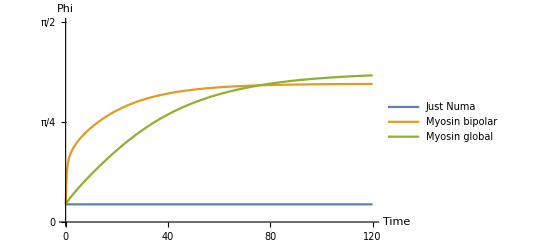

AverageAbsPhi_longer_dynamics.pdf

```mathematica
Plotaverageabsphilongerdynamics=Plot[{avgabsϕNuma[t],avgabsϕMbipolar[t],avgabsϕMglobal[t]},{t,0,120},PlotRange->{0,Pi/2},Ticks->{{0,40,80,120},{0,Pi/4,Pi/2}},TicksStyle->Directive[Black,15],AxesLabel->{Time,Phi},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15],PlotLegends->{"Just Numa", "Myosin bipolar", "Myosin global"}]
Export["AverageAbsPhi_longer_dynamics.pdf",Plotaverageabsphilongerdynamics ,"PDF","AllowRasterization"->False]
```

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

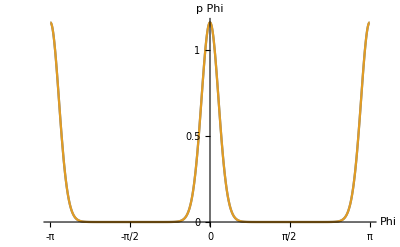

Probability_distributions_Numa_long_time_scale.pdf

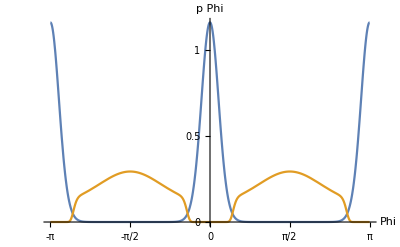

Probability_distributions_Myosinbipolar_long_time_scale.pdf

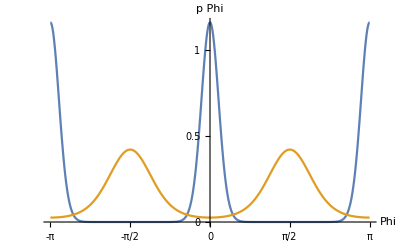

Probability_distributions_Myosinglobal_long_time_scale.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
pdfJustNuma=Plot[{solFPNuma/.{ϕ->ϕ2,t->0.},solFPNuma/.{ϕ->ϕ2,t->120}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Numa_long_time_scale.pdf",pdfJustNuma,"PDF","AllowRasterization"->False] 
pdfmyosin10X10=Plot[{solFPMbipolar/.{ϕ->ϕ2,t->0.},solFPMbipolar/.{ϕ->ϕ2,t->120}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Myosinbipolar_long_time_scale.pdf",pdfmyosin10X10,"PDF","AllowRasterization"->False] 
pdfmyosinglobal=Plot[{solFPMglobal/.{ϕ->ϕ2,t->0.},solFPMglobal/.{ϕ->ϕ2,t->120}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Myosinglobal_long_time_scale.pdf",pdfmyosinglobal,"PDF","AllowRasterization"->False]
```

## Repeat analysis for smaller value of myosinfactor

```mathematica
myosinfactor = 0.4
```

0.4

With this choice, the force distribution stays positive.

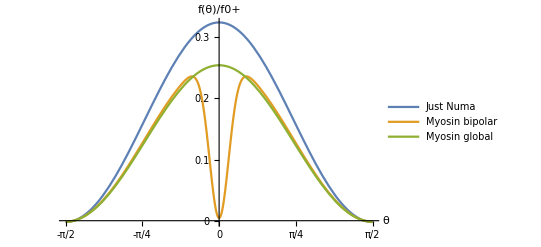

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

ForceDensityPlots_smallermyosinfactor.pdf

```mathematica
ForceDensityPlots=Plot[{gN[θ], gN[θ]*(1-myosinfactor*gMbipolar[θ]),gN[θ]*(1-myosinfactor*gMglobal[θ])},{θ,-Pi/2,Pi/2},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{θ,"f(θ)/f0+"},PlotLegends->{"Just Numa", "Myosin bipolar",  "Myosin global"},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{0,0.1,0.2,0.3}},TicksStyle->Directive[Black,15],LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["ForceDensityPlots_smallermyosinfactor.pdf",ForceDensityPlots ,"PDF","AllowRasterization"->False]
```

Plot the profiles of normalised torques

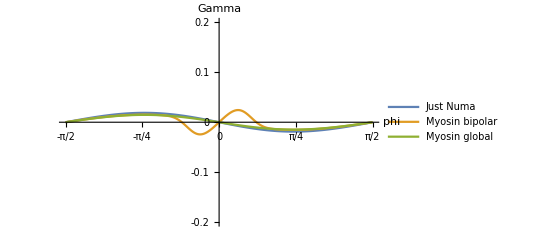

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

TorquePlots_smaller_myosin_factor.pdf

```mathematica
TorquePlots = Plot[{TorqueValueNuma[ϕ,lmvalue,Rvalue,lcvalue], TorqueValueMbipolar[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor ],
TorqueValueMglobal[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor]
},{ϕ,-Pi/2,Pi/2},PlotLegends->{"Just Numa", "Myosin bipolar",  "Myosin global"},PlotRange->{-0.2,0.2},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-0.2,-0.1, 0, 0.1,0.2}},TicksStyle->Directive[Black,15],AxesLabel->{phi,Gamma},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["TorquePlots_smaller_myosin_factor.pdf",TorquePlots ,"PDF","AllowRasterization"->False]
```

-Graphics-

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

TorquePlotNuma_smallermyosinfactor.pdf

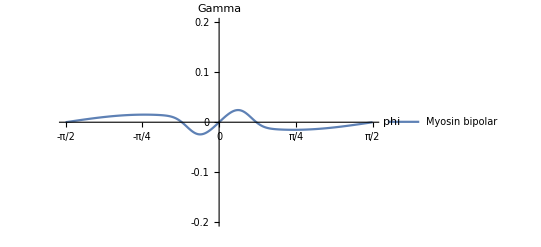

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

TorquePlotMbipolar_smallermyosinfactor.pdf

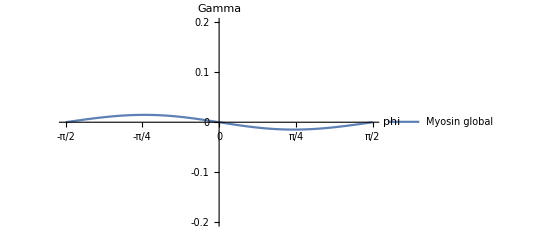

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

TorquePlotMglobal_smallermyosinfactor.pdf

```mathematica
TorquePlotNuma = Plot[{TorqueValueNuma[ϕ,lmvalue,Rvalue,lcvalue]
},{ϕ,-Pi/2,Pi/2},PlotLegends->{"Just Numa"},PlotRange->{-0.2,0.2},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-0.2,-0.1, 0, 0.1,0.2}},TicksStyle->Directive[Black,15],AxesLabel->{phi,Gamma},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["TorquePlotNuma_smallermyosinfactor.pdf",TorquePlotNuma ,"PDF","AllowRasterization"->False] 
TorquePlotMbipolar = Plot[{ TorqueValueMbipolar[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor ]
},{ϕ,-Pi/2,Pi/2},PlotLegends->{ "Myosin bipolar"},PlotRange->{-0.2,0.2},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-0.2,-0.1, 0, 0.1,0.2}},TicksStyle->Directive[Black,15],AxesLabel->{phi,Gamma},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["TorquePlotMbipolar_smallermyosinfactor.pdf",TorquePlotMbipolar ,"PDF","AllowRasterization"->False] 
TorquePlotMglobal = Plot[{TorqueValueMglobal[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor]
},{ϕ,-Pi/2,Pi/2},PlotLegends->{ "Myosin global"},PlotRange->{-0.2,0.2},Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{-0.2,-0.1, 0, 0.1,0.2}},TicksStyle->Directive[Black,15],AxesLabel->{phi,Gamma},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
SetDirectory[NotebookDirectory[]]
Export["TorquePlotMglobal_smallermyosinfactor.pdf",TorquePlotMglobal  ,"PDF","AllowRasterization"->False]
```

```mathematica
Measuredoneoverbartauvalue  = 0.20508;
MeasuredDiffusionCoefficient = 19.265;
DiffusionCoefficientRad = MeasuredDiffusionCoefficient *(Pi/180)^2
Dvalue=DiffusionCoefficientRad ;
```

0.00586845

```mathematica
TorqueFunctionNuma[ϕ_?NumberQ]:= TorqueValueNuma[ϕ,lmvalue,Rvalue,lcvalue];
TorqueFunctionMbipolar[ϕ_?NumberQ]:=  TorqueValueMbipolar[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor];
TorqueFunctionMglobal[ϕ_?NumberQ]:=TorqueValueMglobal[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor];
```

## Run spindle dynamics - stochastic (Fokker-Planck) - with experimentally determined diffusion and linear response time

Experimental measurements from mean squared rotations
The value of one over bar{tau} is in 1/minute
The measured Diffusion coefficient is in deg^2/min
It is then converted below in radians^2/min

```mathematica
Measuredoneoverbartauvalue  = 0.20508;
MeasuredDiffusionCoefficient = 19.265;
DiffusionCoefficientRad = MeasuredDiffusionCoefficient *(Pi/180)^2
Dvalue=DiffusionCoefficientRad ;
```

0.00586845

```mathematica
TorqueFunctionNuma[ϕ_?NumberQ]:= TorqueValueNuma[ϕ,lmvalue,Rvalue,lcvalue];
TorqueFunctionMbipolar[ϕ_?NumberQ]:=  TorqueValueMbipolar[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor];
TorqueFunctionMglobal[ϕ_?NumberQ]:=TorqueValueMglobal[ϕ,lmvalue,Rvalue,lcvalue,myosinfactor];
```

Value of the linear torque response for the Numa case

```mathematica
Needs["NumericalCalculus`"]
LinearResponseFactor =-ND[TorqueFunctionNuma[ϕ],ϕ,0]
```

0.0392383

This allows to obtain an estimate of τ=γ/Γ0 by relating it to \bar{tau}”

```mathematica
τ=LinearResponseFactor/Measuredoneoverbartauvalue
```

0.191332

(Arbitrary) initial condition to solve the Fokker Planck equation

```mathematica
p0[ϕ_]=1/2*(PDF[VonMisesDistribution[0,1/0.1^2],ϕ]+PDF[VonMisesDistribution[0,1/0.1^2],Pi-ϕ]+PDF[VonMisesDistribution[0,1/0.1^2],ϕ+Pi]);
```

```mathematica
Plot[p0[ϕ],{ϕ,-Pi,Pi},PlotRange->All]
```

-Graphics-

Interpolate the torque function to accelerate solving

```mathematica
PrecisionInterpolation=10^(-4);
```

```mathematica
TorqueFunctionNumaTable=Table[{ϕ,TorqueFunctionNuma[ϕ]},{ϕ,-3.5,3.5,PrecisionInterpolation}];
TorqueFunctionNumaInterp=Interpolation[TorqueFunctionNumaTable];
TorqueFunctionMbipolarTable=Table[{ϕ,TorqueFunctionMbipolar[ϕ]},{ϕ,-3.5,3.5,PrecisionInterpolation}];
TorqueFunctionMbipolarInterp=Interpolation[TorqueFunctionMbipolarTable];
TorqueFunctionMglobalTable=Table[{ϕ,TorqueFunctionMglobal[ϕ]},{ϕ,-3.5,3.5,PrecisionInterpolation}];
TorqueFunctionMglobalInterp=Interpolation[TorqueFunctionMglobalTable];
```

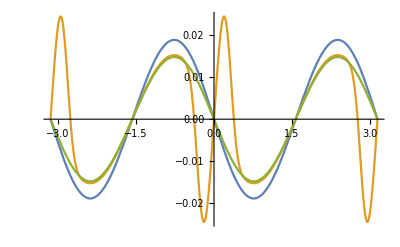

```mathematica
Plot[{TorqueFunctionNumaInterp[ϕ],TorqueFunctionMbipolarInterp[ϕ],TorqueFunctionMglobalInterp[ϕ]},{ϕ,-Pi,Pi},PlotRange->All]
```

First solve the evolution of the probability distribution for Numa
The corresponding equilibrium distribution will be used as the initialisation for other conditions

```mathematica
solFPNuma=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionNumaInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==p0[ϕ]},p[ϕ,t],{t,0,100},{ϕ,-Pi,Pi},PrecisionGoal->8,AccuracyGoal->6][[1]]
```

InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 100.}}, <>][ϕ,t]

```mathematica
Plot[{solFPNuma/.{ϕ->ϕ2,t->0.},solFPNuma/.{ϕ->ϕ2,t->50},solFPNuma/.{ϕ->ϕ2,t->100}},{ϕ2,-Pi,Pi},PlotRange->All]
```

-Graphics-

Restart with the equilibrium configuration with just Numa

```mathematica
newp0[ϕ2_]=solFPNuma/.{ϕ->ϕ2,t->100}
```

InterpolatingFunction[{{…, -3.14159, 3.14159, …}, {0., 100.}}, <>][ϕ2,100]

```mathematica
solFPNuma=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionNumaInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,12},{ϕ,-Pi,Pi}][[1]];
solFPMbipolar=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionMbipolarInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,12},{ϕ,-Pi,Pi}, Method->{"PDEDiscretization"->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->1000}}}][[1]];
solFPMglobal=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionMglobalInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,12},{ϕ,-Pi,Pi}][[1]];
```

-Graphics-

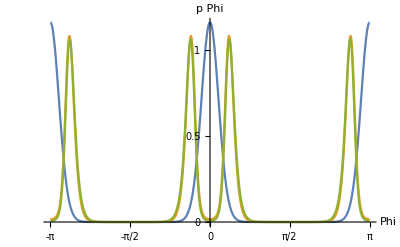

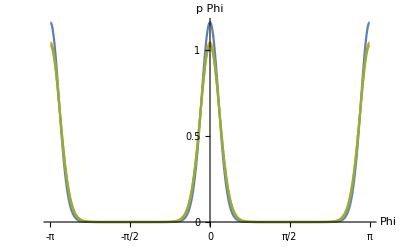

```mathematica
Plot[{solFPNuma/.{ϕ->ϕ2,t->0.},solFPNuma/.{ϕ->ϕ2,t->6},solFPNuma/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Plot[{solFPMbipolar/.{ϕ->ϕ2,t->0.},solFPMbipolar/.{ϕ->ϕ2,t->6},solFPMbipolar/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Plot[{solFPMglobal/.{ϕ->ϕ2,t->0.},solFPMglobal/.{ϕ->ϕ2,t->6},solFPMglobal/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
```

Plot the result between -Pi/2 and Pi/2

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

-Graphics-

Probability_distributions_Numa_smallermyosinfactor.pdf

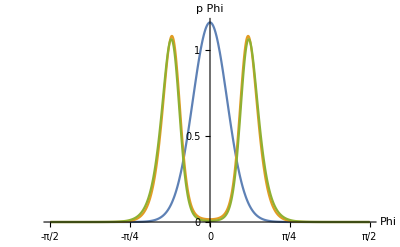

Probability_distributions_Myosin10X10_smallermyosinfactor.pdf

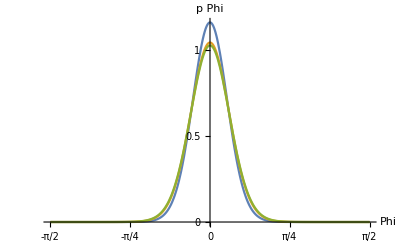

Probability_distributions_Myosinglobal_smallermyosinfactor.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
pdfJustNuma=Plot[{solFPNuma/.{ϕ->ϕ2,t->0.},solFPNuma/.{ϕ->ϕ2,t->6},solFPNuma/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi/2,Pi/2},PlotRange->All,Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Numa_smallermyosinfactor.pdf",pdfJustNuma,"PDF","AllowRasterization"->False] 
pdfmyosin10X10=Plot[{solFPMbipolar/.{ϕ->ϕ2,t->0.},solFPMbipolar/.{ϕ->ϕ2,t->6},solFPMbipolar/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi/2,Pi/2},PlotRange->All,Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Myosin10X10_smallermyosinfactor.pdf",pdfmyosin10X10,"PDF","AllowRasterization"->False] 
pdfmyosinglobal=Plot[{solFPMglobal/.{ϕ->ϕ2,t->0.},solFPMglobal/.{ϕ->ϕ2,t->6},solFPMglobal/.{ϕ->ϕ2,t->12}},{ϕ2,-Pi/2,Pi/2},PlotRange->All,Ticks->{{-Pi/2,-Pi/4,0,Pi/4,Pi/2},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Myosinglobal_smallermyosinfactor.pdf",pdfmyosinglobal,"PDF","AllowRasterization"->False]
```

Plot the average value of ϕ between 0 and pi/2

```mathematica
avgabsϕNuma[t2_?NumberQ]:=NIntegrate[ϕ solFPNuma/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPNuma/.{t->t2},{ϕ,0,Pi/2}]
avgabsϕMbipolar[t2_?NumberQ]:=NIntegrate[ϕ solFPMbipolar/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPMbipolar/.{t->t2},{ϕ,0,Pi/2}]
avgabsϕMglobal[t2_?NumberQ]:=NIntegrate[ϕ solFPMglobal/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPMglobal/.{t->t2},{ϕ,0,Pi/2}]
```

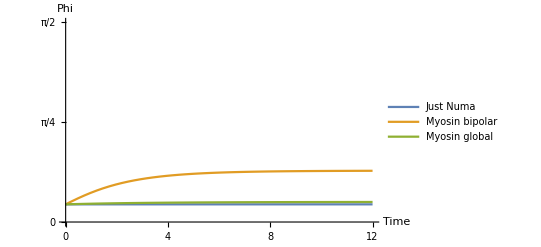

AverageAbsPhi_smallermyosinfactor.pdf

```mathematica
Plotaverageabsphi=Plot[{avgabsϕNuma[t],avgabsϕMbipolar[t],avgabsϕMglobal[t]},{t,0,12},PlotRange->{0,Pi/2},Ticks->{{0,4,8,12},{0,Pi/4,Pi/2}},TicksStyle->Directive[Black,15],AxesLabel->{Time,Phi},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15],PlotLegends->{"Just Numa", "Myosin bipolar", "Myosin global"}]
Export["AverageAbsPhi_smallermyosinfactor.pdf",Plotaverageabsphi ,"PDF","AllowRasterization"->False]
```

## Evolution on a longer time scale (smaller myosin factor)

```mathematica
solFPNuma=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionNumaInterp[ϕ] p[ϕ,t],ϕ]+τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,120},{ϕ,-Pi,Pi}][[1]];
solFPMbipolar=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionMbipolarInterp[ϕ] p[ϕ,t],ϕ]+τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,120},{ϕ,-Pi,Pi}, Method->{"PDEDiscretization"->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->1000}}}][[1]];
solFPMglobal=p[ϕ,t]/.NDSolve[{τ D[p[ϕ,t],t]==-D[TorqueFunctionMglobalInterp[ϕ] p[ϕ,t],ϕ]+ τ Dvalue D[p[ϕ,t],{ϕ,2}] ,p[-Pi,t]==p[Pi,t], p[ϕ,0]==newp0[ϕ]},p[ϕ,t],{t,0,120},{ϕ,-Pi,Pi}][[1]];
```

```mathematica
avgabsϕNuma[t2_?NumberQ]:=NIntegrate[ϕ solFPNuma/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPNuma/.{t->t2},{ϕ,0,Pi/2}]
avgabsϕMbipolar[t2_?NumberQ]:=NIntegrate[ϕ solFPMbipolar/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPMbipolar/.{t->t2},{ϕ,0,Pi/2}]
avgabsϕMglobal[t2_?NumberQ]:=NIntegrate[ϕ solFPMglobal/.{t->t2},{ϕ,0,Pi/2}]/NIntegrate[solFPMglobal/.{t->t2},{ϕ,0,Pi/2}]
```

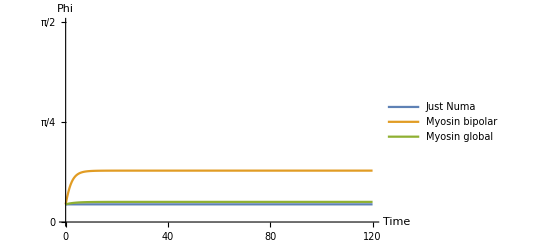

AverageAbsPhi_longer_dynamics_smallermyosinfactor.pdf

```mathematica
Plotaverageabsphilongerdynamics=Plot[{avgabsϕNuma[t],avgabsϕMbipolar[t],avgabsϕMglobal[t]},{t,0,120},PlotRange->{0,Pi/2},Ticks->{{0,40,80,120},{0,Pi/4,Pi/2}},TicksStyle->Directive[Black,15],AxesLabel->{Time,Phi},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15],PlotLegends->{"Just Numa", "Myosin bipolar", "Myosin global"}]
Export["AverageAbsPhi_longer_dynamics_smallermyosinfactor.pdf",Plotaverageabsphilongerdynamics ,"PDF","AllowRasterization"->False]
```

/Users/salbreux/Dropbox (The Francis Crick)/Spindle_Myosin/Data analysis/Mathematica

-Graphics-

Probability_distributions_Numa_long_time_scale_smallermyosinfactor.pdf

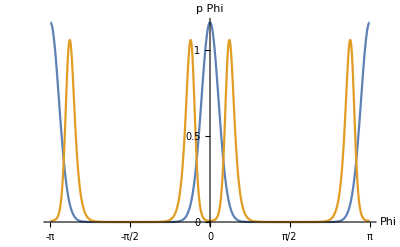

Probability_distributions_Myosinbipolar_long_time_scale_smallermyosinfactor.pdf

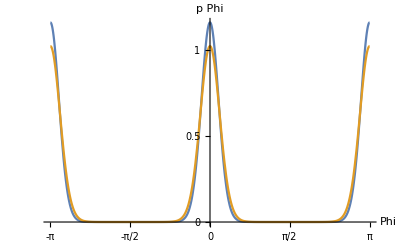

Probability_distributions_Myosinglobal_long_time_scale_smallermyosinfactor.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
pdfJustNuma=Plot[{solFPNuma/.{ϕ->ϕ2,t->0.},solFPNuma/.{ϕ->ϕ2,t->120}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Numa_long_time_scale_smallermyosinfactor.pdf",pdfJustNuma,"PDF","AllowRasterization"->False] 
pdfmyosin10X10=Plot[{solFPMbipolar/.{ϕ->ϕ2,t->0.},solFPMbipolar/.{ϕ->ϕ2,t->120}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Myosinbipolar_long_time_scale_smallermyosinfactor.pdf",pdfmyosin10X10,"PDF","AllowRasterization"->False] 
pdfmyosinglobal=Plot[{solFPMglobal/.{ϕ->ϕ2,t->0.},solFPMglobal/.{ϕ->ϕ2,t->120}},{ϕ2,-Pi,Pi},PlotRange->All,Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},{0,0.5,1}},TicksStyle->Directive[Black,15],AxesLabel->{Phi,p(Phi)},LabelStyle->Directive[Black,15],AxesStyle->Directive[Black,15]]
Export["Probability_distributions_Myosinglobal_long_time_scale_smallermyosinfactor.pdf",pdfmyosinglobal,"PDF","AllowRasterization"->False]
```